```mathematica
(*Cèsar Muro Cabral*)
```

## Run this line.

```mathematica
Needs["FourierSeries`"];
```

## In this first section, we analyze Electromganetically induced transparency in the case of an ensemble of cold atoms of Rubidium 87 in the D2 - line, where the atoms are pumping to the Zeeman sublevel m = 1. We employ an initial Gaussian pulse of Tp=0.500, ζ=2.0, hp54=251Mhz, and Γ=6.065. The dipole moment of the control field is attached to F=2,m=2→F’=2,m=2 and its Rabi frequency is written as Rabi=√((OD*Γ)/(ζ*Tp)). We obtain and solve the Bloch equations, plot the absorption Im[χ], the dispersion Re[χ] and the transmission with and optical depth OD of OD=275:

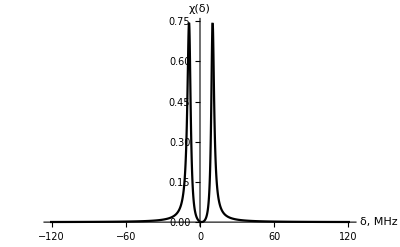

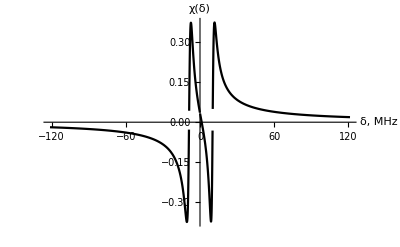

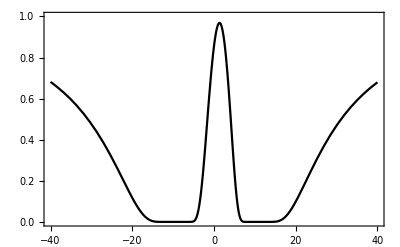

```mathematica
Γ=6.065;
j=3/2;
S=1/2;
IS=3/2;
hbar=1;
gfe4=0.93;
gfg=-0.70;
gfs=0.70;
m=2;
γ21=0.0001*Γ;
hpf32=266.65;
γ31=0.5*Γ;
γ41=0.5*Γ;
OD=Table[OD=od ;OD,{od,0.00001,600,4}];
L001=Length[OD];
Tp=0.500;
ζ=2.0;
hbar=1;
Rabi=√((OD*Γ)/(ζ*Tp));
Vp[Fe_,me_,Fg_,mg_]:=√(3/4*hbar*(2*j+1)*(2*Fg+1))*ClebschGordan[{Fg,mg},{1,me-mg},{Fe,me}]*SixJSymbol[{S,IS,Fg},{Fe,1,j}]*√Γ;

Vc[Fe_,me_,Fs_,ms_]:=((ClebschGordan[{Fs,ms},{1,me-ms},{Fe,me}]*SixJSymbol[{S,IS,Fs},{Fe,1,j}])/(ClebschGordan[{2,1},{1,1},{2,2}]*SixJSymbol[{S,IS,Fs},{2,1,j}]))*Rabi/2;
MatrixForm[sys3={{Subscript[ρ, g3g3],Subscript[ρ, g3s3],Subscript[ρ, g3e4],Subscript[ρ, g3e5]},{Subscript[ρ, s3g3],Subscript[ρ, s3s3],Subscript[ρ, s3e4],Subscript[ρ, s3e5]},{Subscript[ρ, e4g3],Subscript[ρ, e4s3],Subscript[ρ, e4e4],Subscript[ρ, e4e5]},{Subscript[ρ, e5g3],Subscript[ρ, e5s3],Subscript[ρ, e5e4],Subscript[ρ, e5e5]}}];
MatrixForm[h7={{0,0,Subscript[ΩP, g3e4],0},{0,-Δc+Δp,Subscript[ΩC, s3e4],Subscript[ΩC, s3e5]},{Subscript[ΩP, g3e4],Subscript[ΩC, s3e4],+Δp,0},{0,Subscript[ΩC, s3e5],0,hpf32-Δc+Δp}}];
TableForm[dt1={{0,0,0,0},{0,γ21,0,0},{0,0,γ31,0},{0,0,0,γ41}}];
TableForm[leqs3=(I*(h7.sys3-sys3.h7))+dt1.sys3];
solg3=Solve[{leqs3[[2,1]]==-I*ω*Subscript[ρ, s3g3],leqs3[[3,1]]==-I*ω*Subscript[ρ, e4g3],leqs3[[4,1]]==-I*ω*Subscript[ρ, e5g3],Subscript[χ, g4l]==-Simplify[(Subscript[ρ, e4g3]*Subscript[ΩP, g3e4])]},{Subscript[ρ, s3g3],Subscript[ρ, e4g3],Subscript[ρ, e5g3],Subscript[χ, g4l]}]/.{Subscript[ρ, s3e4]->0,Subscript[ρ, e4e4]->0,Subscript[ρ, e5s3]->0,Subscript[ρ, e5e4]->0,Subscript[ρ, g3g3]->1};
Subscript[χ, pol4l]=Chop@Subscript[χ, g4l]/.solg3/.{Subscript[ΩC, s3e4]->Vc[2,2,2,1],Subscript[ΩC, s3e5]->Vc[3,2,2,1],Subscript[ΩP, g3e4]->Vp[2,2,1,1]};

Plot[{Evaluate[Im[Subscript[χ, pol4l][[1]][[16]]]/.{Δc->0,ω->0}]},{Δp,-20*Γ,20*Γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]
Plot[{Evaluate[Re[Subscript[χ, pol4l][[1]][[16]]]/.{Δc->0,ω->0}]},{Δp,-20*Γ,20*Γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]

Plot[Exp[-((Γ/2)*OD[[16]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[16]]/.{Δc->0,ω->0})]]],{Δp,-40,40},PlotStyle->Black,PlotRange->{0,1.0},Frame->True]
```

## Now we construct a table called “det”, with the detunings Δp’s where the transmission achieves the maximum for each optical depth.

```mathematica
det=Table[Δp/.Last[FindMaximum[{Exp[-((Γ/2)*OD[[i]])*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,ΔD->0,ω->0})]]],-50<=Δp<=0},{Δp,-1}]],{i,1,L001}]
```

{-10.4141,-0.316885,-0.6323,-0.946267,-1.25881,-1.56994,-1.87968,-2.18805,-2.49506,-2.80075,-3.10511,-3.40818,-3.70996,-4.01048,-4.30975,-4.60778,-4.90459,-5.2002,-5.49463,-5.78787,-6.07996,-6.3709,-6.66071,-6.9494,-7.23699,-7.52348,-7.80889,-8.09324,-8.37652,-8.65877,-8.93999,-9.22018,-9.49937,-9.77756,-10.0548,-10.331,-10.6062,-10.8806,-11.1539,-11.4263,-11.6978,-11.9684,-12.2381,-12.5069,-12.7748,-13.0418,-13.308,-13.5733,-13.8377,-14.1013,-14.3641,-14.626,-14.8871,-15.1474,-15.4069,-15.6657,-15.9236,-16.1807,-16.4371,-16.6927,-16.9475,-17.2016,-17.455,-17.7076,-17.9595,-18.2107,-18.4611,-18.7108,-18.9599,-19.2082,-19.4558,-19.7028,-19.949,-20.1946,-20.4396,-20.6838,-20.9274,-21.1704,-21.4127,-21.6543,-21.8954,-22.1358,-22.3755,-22.6147,-22.8532,-23.0912,-23.3285,-23.5652,-23.8013,-24.0369,-24.2718,-24.5062,-24.74,-24.9732,-25.2059,-25.438,-25.6695,-25.9005,-26.1309,-26.3608,-26.5901,-26.8189,-27.0472,-27.2749,-27.5021,-27.7288,-27.955,-28.1806,-28.4058,-28.6304,-28.8545,-29.0782,-29.3013,-29.5239,-29.7461,-29.9678,-30.1889,-30.4096,-30.6299,-30.8496,-31.0689,-31.2877,-31.5061,-31.724,-31.9414,-32.1584,-32.3749,-32.591,-32.8066,-33.0218,-33.2366,-33.4509,-33.6648,-33.8782,-34.0913,-34.3039,-34.5161,-34.7278,-34.9392,-35.1501,-35.3606,-35.5707,-35.7804,-35.9897,-36.1986,-36.4071,-36.6152,-36.8229,-37.0302,-37.2371,-37.4437,-37.6498,-37.8556,-38.061,-38.266,-38.4706,-38.6749,-38.8788,-39.0823,-39.2855,-39.4883,-39.6907,-39.8928,-40.0945,-40.2958,-40.4968,-40.6975,-40.8977,-41.0977,-41.2973,-41.4965,-41.6955,-41.894,-42.0923,-42.2902,-42.4877,-42.6849,-42.8818,-43.0784,-43.2746,-43.4705,-43.6661,-43.8614,-44.0563,-44.2509,-44.4452,-44.6392,-44.8329,-45.0263,-45.2193,-45.4121,-45.6045,-45.7966,-45.9884,-46.18,-46.3712,-46.5621,-46.7527,-46.943,-47.1331}

## We write the inital pulse as Wp0[ω]= Tp/(√(4Log[2]))*Exp[(-ω^2 Tp^2)/(8*Log[2])]. To compute the storage-efficiency, we analyze two equivalent approaches: -integrating in ω-frequency domain and - numerical Fourier transform. We construct the output pulse as ϵ_out=Wp0[ω]*Exp[-((Γ/2)*OD[[i]]/(Vp[4,4,3,3]^2))*Evaluate[Im[(χ_pol4l[[1]][[i]]/.{Δc→0,ΔD->0,Δp->det[[i]]})]]], and the efficiency of the optical memory is estimated as (∫_(-∞)^∞ |ϵ_out|^2 ⅆω)/(∫_(-∞)^∞ |ϵ_in|^2 ⅆω) , and (∫_(-∞)^∞ |ϵ_out|^2 ⅆt)/(∫_(-∞)^∞ |ϵ_in|^2 ⅆt).Therefore

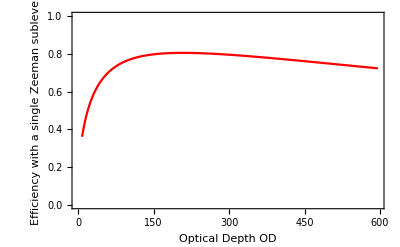

```mathematica
det=Table[Δp/.Last[FindMaximum[{Exp[-((Γ/2)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,ω->0})]]],0<=Δp<=35},{Δp,1}]],{i,1,L001}];
Wp0[ω_]:=Tp/(√(4Log[2]))*Exp[(-ω^2 Tp^2)/(8*Log[2])];
(*I store the out pulse in a table being every element the corresponding for for every optical depth*)
ϵ3d2out=Table[Wp0[ω]*Exp[-((Γ/4)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,Δp->det[[i]]})]]],{i,1,L001}];
(*Then I follow the formula (14) for the the slow light transmission efficiency  "Broadband coherent optical memory"*)
eff4l=Table[NIntegrate[Abs[ϵ3d2out[[i]]]^2,{ω,-∞,∞}]/NIntegrate[Abs[Wp0[ω]]^2,{ω,-∞,∞}],{i,1,L001}];
data4l=Transpose@{OD,eff4l};
(*As you can see large optical depth*)
ListPlot[Delete[data4l,{{1},{2}}],Frame->True,PlotRange->{All,{0,1.0}},Joined->True,PlotStyle->{Black,Red},FrameLabel->{"Optical Depth OD","Efficiency with a single Zeeman sublevel"}]
```

## Numerical Fourier Transform function throught Mathematica function NInverseFourier transform. We have to run the first line of the code. The time interval where we calculate the Fourier transform (thus the efficiency) is from -6 to 6, in steps size of 0.25.

```mathematica
τ=Table[τ=tim;τ,{tim,-6,6,0.25}];
OD=Table[OD=od ;OD,{od,0.00001,600,4}];
Wp0[ω_]:=Tp/(√(4Log[2]))*Exp[(-ω^2 Tp^2)/(8*Log[2])];
L001=Length[OD];
det=Table[Δp/.Last[FindMaximum[{Exp[-((Γ/2)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,ω->0})]]],0<=Δp<=35},{Δp,1}]],{i,1,L001}];

ϵ3d2out=Table[Wp0[ω]*Exp[-((Γ/4)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,Δp->det[[i]]})]]],{i,1,L001}];
ft4l=Table[Chop@NInverseFourierTransform[ϵ3d2out[[h]],ω,i],{h,2,L001},{i,-6,6,.25}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {2.74411}. NIntegrate obtained 4.34702×10^-10-8.59438×10^-11 ⅈ and 5.80554×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.71493×10^-10+1.98263×10^-10 ⅈ and 3.88714×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.71493×10^-10-1.98263×10^-10 ⅈ and 3.88714×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.00131×10^-10+4.03265×10^-12 ⅈ and 3.89273×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
ϵsZ=Transpose@{Delete[OD,{{1}}],Chop@Table[NIntegrate[(Interpolation[Transpose@{τ,ft4l[[i]]},InterpolationOrder->3][t])^2,{t,-8,8}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,Length[ft4l]}]}
ListPlot[{Delete[data4l,{{1},{2}}],Insert[ϵsZ,{0,0},1]},Joined->True,PlotRange->{0,1.0},Frame->True,FrameTicksStyle->Directive[Black,18]]
```

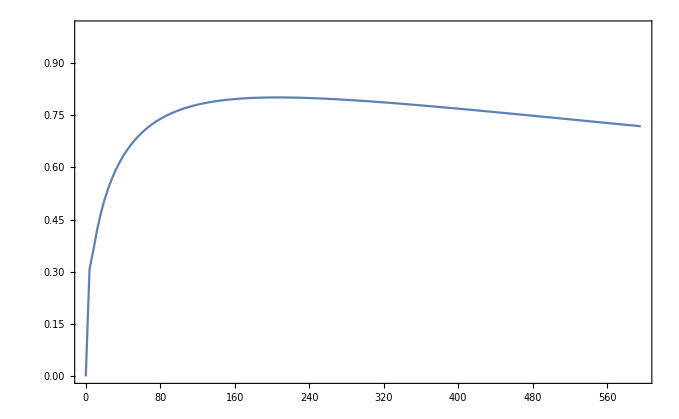

```mathematica
ListPlot[{Insert[ϵsZ,{0,0},1]},Joined->True,PlotRange->{0,1.0},Frame->True,FrameTicksStyle->Directive[Black,18],PlotRangePadding->None]
```

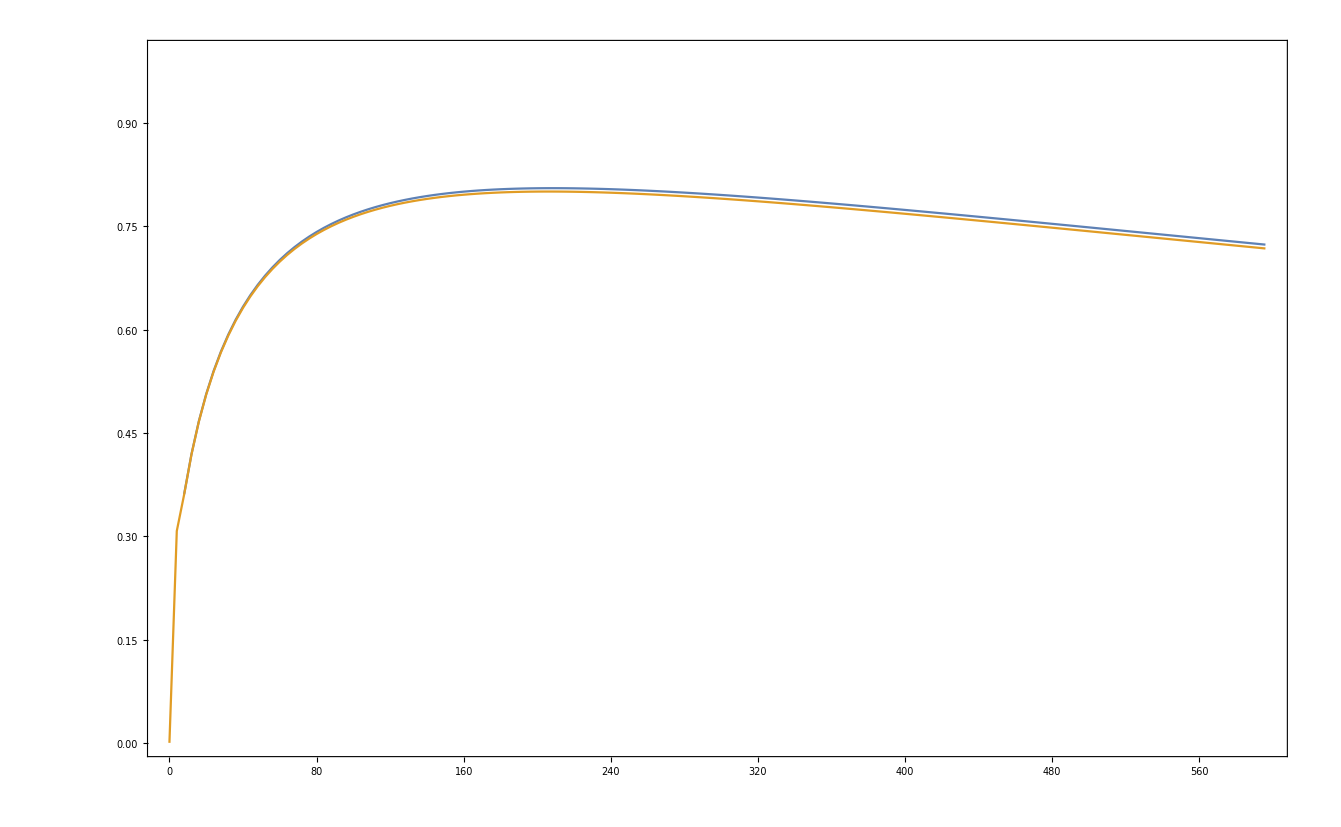

```mathematica
ListPlot[{Delete[data4l,{{1},{2}}],Insert[ϵsZ,{0,0},1]},Joined->True,PlotRange->{0,1.0},Frame->True,FrameTicksStyle->Directive[Black,18]]
```

# Let us analyze now the case with all Zeeman sublevels, we define again the parameters involved, and solve for every sublevel

```mathematica
(*Initial parameters*)

Fg=1;
Fs=2;
Fe3=3;
Fe2=2;
Fe1=1;
Fe0=0;
S=1/2;
IS=3/2;
j=3/2;
γ=6.065;
Γ=6.065;
Tp=0.500;
ζ=2.0;
(*2.7*)
OD=Table[OD=od ;OD,{od,0.00001,600,2}];
L001=Length[OD];
Rabi=√((OD*Γ)/(ζ*Tp)) ;
γsg=0.001*γ;
hbar = 1;
hpf12=-156.94;
hpf32=266.65;
hpf02=-(72.218+156.94);
```

```mathematica
Vp[Fe_,me_,Fg_,mg_]:=√((3/4)*hbar*(2*j+1)*(2*Fg+1))*ClebschGordan[{Fg,mg},{1,me-mg},{Fe,me}]*SixJSymbol[{S,IS,Fg},{Fe,1,j}]*√γ;

Vc[Fe_,me_,Fs_,ms_]:=((ClebschGordan[{Fs,ms},{1,me-ms},{Fe,me}]*SixJSymbol[{S,IS,Fs},{Fe,1,j}])/(ClebschGordan[{2,0},{1,1},{2,1}]*SixJSymbol[{S,IS,Fs},{2,1,j}]))*Rabi/2;
```

```mathematica
mgm1=-1;
MatrixForm[sysm1={{Subscript[ρ, gg],Subscript[ρ, gs],Subscript[ρ, ge2],Subscript[ρ, ge3],Subscript[ρ, ge4],Subscript[ρ, ge5]},{Subscript[ρ, sg],Subscript[ρ, ss],Subscript[ρ, se2],Subscript[ρ, se3],Subscript[ρ, se4],Subscript[ρ, se5]},{Subscript[ρ, e2g],Subscript[ρ, e2s],Subscript[ρ, e2e2],Subscript[ρ, e2e3],Subscript[ρ, e2e4],Subscript[ρ, e2e5]},{Subscript[ρ, e3g],Subscript[ρ, e3s],Subscript[ρ, e3e2],Subscript[ρ, e3e3],Subscript[ρ, e3e4],Subscript[ρ, e3e5]},{Subscript[ρ, e4g],Subscript[ρ, e4s],Subscript[ρ, e4e2],Subscript[ρ, e4e3],Subscript[ρ, e4e4],Subscript[ρ, e4e5]},{Subscript[ρ, e5g],Subscript[ρ, e5s],Subscript[ρ, e5e2],Subscript[ρ, e5e3],Subscript[ρ, e5e4],Subscript[ρ, e5e5]}}];
MatrixForm[h1={{0,0,Vpe2,Vpe3,Vpe4,0},{0,-Δc+Δp,0,ΩCe3s,ΩCe4s,ΩCe5s},{Vpe2,0,hpf02+Δp,0,0,0},{Vpe3,ΩCe3s,0,hpf12+Δp,0,0},{Vpe4,ΩCe4s,0,0,+Δp,0},{0,ΩCe5s,0,0,0,hpf32+Δp}}];
TableForm[dt1={{0,0,0,0,0,0},{0,γsg,0,0,0,0},{0,0,γ/2,0,0,0},{0,0,0,γ/2,0,0},{0,0,0,0,γ/2,0},{0,0,0,0,0,γ/2}}];
TableForm[leqsm1=I*(h1.sysm1-sysm1.h1)+dt1.sysm1];
solmgm1=Solve[{leqsm1[[2,1]]==-I*ω*Subscript[ρ, sg],leqsm1[[3,1]]==-I*ω*Subscript[ρ, e2g],leqsm1[[4,1]]==-I*ω*Subscript[ρ, e3g],leqsm1[[5,1]]==-I*ω*Subscript[ρ, e4g],leqsm1[[6,1]]==-I*ω*Subscript[ρ, e5g],Subscript[χ, mgm1]==-(Vp[Fe1,mgm1+1,Fg,mgm1]*Subscript[ρ, e3g]+Vp[Fe2,mgm1+1,Fg,mgm1]*Subscript[ρ, e4g]+Vp[Fe0,mgm1+1,Fg,mgm1]*Subscript[ρ, e2g])},{Subscript[ρ, sg],Subscript[ρ, e2g],Subscript[ρ, e3g],Subscript[ρ, e4g],Subscript[ρ, e5g],Subscript[χ, mgm1]}]/.{Subscript[ρ, e2e2]->0,Subscript[ρ, e2e3]->0,Subscript[ρ, e2e4]->0,Subscript[ρ, e3e2]->0,Subscript[ρ, e3e3]->0,Subscript[ρ, e3e4]->0,Subscript[ρ, e4e2]->0,Subscript[ρ, e4e3]->0,Subscript[ρ, e4e4]->0,Subscript[ρ, e5e2]->0,Subscript[ρ, e5e3]->0,Subscript[ρ, e5e4]->0,Subscript[ρ, se2]->0,Subscript[ρ, se3]->0,Subscript[ρ, se4]->0};
χpolmgm1=Subscript[χ, mgm1]/.solmgm1/.{Vpe2->Vp[Fe0,mgm1+1,Fg,mgm1],Vpe3->Vp[Fe1,mgm1+1,Fg,mgm1],Vpe4->Vp[Fe2,mgm1+1,Fg,mgm1],ΩCe3s->Vc[Fe1,mgm1+1,Fs,mgm1],ΩCe4s->Vc[Fe2,mgm1+1,Fs,mgm1],ΩCe5s->Vc[Fe3,mgm1+1,Fs,mgm1],Subscript[ρ, gg]->1/3};
```

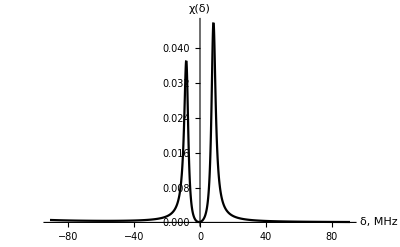

```mathematica
Plot[{Evaluate[Evaluate[Im[χpolmgm1[[1]][[10]]]]/.{Δc->0,ω->0}]},{Δp,-15γ,15γ},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->All,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]
```

```mathematica
mg0=0;
MatrixForm[sys0={{Subscript[ρ, gg],Subscript[ρ, gs],Subscript[ρ, ge1],Subscript[ρ, ge2],Subscript[ρ, ge3]},{Subscript[ρ, sg],Subscript[ρ, ss],Subscript[ρ, se1],Subscript[ρ, se2],Subscript[ρ, se3]},{Subscript[ρ, e1g],Subscript[ρ, e1s],Subscript[ρ, e1e1],Subscript[ρ, e1e2],Subscript[ρ, e1e3]},{Subscript[ρ, e2g],Subscript[ρ, e2s],Subscript[ρ, e2e1],Subscript[ρ, e2e2],Subscript[ρ, e3e3]},{Subscript[ρ, e3g],Subscript[ρ, e3s],Subscript[ρ, e3e1],Subscript[ρ, e3e2],Subscript[ρ, e3e3]}}];
MatrixForm[h1={{0,0,Vpe1,Vpe2,0},{0,-Δc+Δp,ΩCe1s,ΩCe2s,ΩCe3s},{Vpe1,ΩCe1s,hpf12+Δp,0,0},{Vpe2,ΩCe2s,0,Δp,0},{0,ΩCe3s,0,0,hpf32+Δp}}];
TableForm[dt1={{0,0,0,0,0},{0,γsg,0,0,0},{0,0,γ/2,0,0},{0,0,0,γ/2,0},{0,0,0,0,γ/2}}];
TableForm[leqs0=I*(h1.sys0-sys0.h1)+dt1.sys0]
solmg0=Solve[{leqs0[[2,1]]==-I*ω*Subscript[ρ, sg],leqs0[[3,1]]==-I*ω*Subscript[ρ, e1g],leqs0[[4,1]]==-I*ω*Subscript[ρ, e2g],leqs0[[5,1]]==-I*ω*Subscript[ρ, e3g],Subscript[χ, mg0]==-(Vp[Fe1,mg0+1,Fg,mg0]*Subscript[ρ, e1g]+Vp[Fe2,mg0+1,Fg,mg0]*Subscript[ρ, e2g])},{Subscript[ρ, sg],Subscript[ρ, e1g],Subscript[ρ, e2g],Subscript[ρ, e3g],Subscript[χ, mg0]}]/.{Subscript[ρ, e1e1]->0,Subscript[ρ, e1e2]->0,Subscript[ρ, e1e3]->0,Subscript[ρ, e2e1]->0,Subscript[ρ, e2e2]->0,Subscript[ρ, e2e3]->0,Subscript[ρ, e3e1]->0,Subscript[ρ, e3e2]->0,Subscript[ρ, e3e3]->0,Subscript[ρ, se1]->0,Subscript[ρ, se2]->0,Subscript[ρ, se3]->0};
χpolmg0=Subscript[χ, mg0]/.solmg0/.{Vpe1->Vp[Fe1,mg0+1,Fg,mg0],Vpe2->Vp[Fe2,mg0+1,Fg,mg0],ΩCe1s->Vc[Fe1,mg0+1,Fs,mg0],ΩCe2s->Vc[Fe2,mg0+1,Fs,mg0],ΩCe3s->Vc[Fe3,mg0+1,Fs,mg0],Subscript[ρ, gg]->1/3};
```

ⅈ (Vpe1 ρ_e1g+Vpe2 ρ_e2g-Vpe1 ρ_ge1-Vpe2 ρ_ge2) | ⅈ (Vpe1 ρ_e1s+Vpe2 ρ_e2s-ΩCe1s ρ_ge1-ΩCe2s ρ_ge2-ΩCe3s ρ_ge3-(-Δc+Δp) ρ_gs) | ⅈ (Vpe1 ρ_e1e1+Vpe2 ρ_e2e1-(-156.94+Δp) ρ_ge1-Vpe1 ρ_gg-ΩCe1s ρ_gs) | ⅈ (Vpe1 ρ_e1e2+Vpe2 ρ_e2e2-Δp ρ_ge2-Vpe2 ρ_gg-ΩCe2s ρ_gs) | ⅈ (Vpe1 ρ_e1e3+Vpe2 ρ_e3e3-(266.65+Δp) ρ_ge3-ΩCe3s ρ_gs)
0.006065 ρ_sg+ⅈ (ΩCe1s ρ_e1g+ΩCe2s ρ_e2g+ΩCe3s ρ_e3g-Vpe1 ρ_se1-Vpe2 ρ_se2+(-Δc+Δp) ρ_sg) | ⅈ (ΩCe1s ρ_e1s+ΩCe2s ρ_e2s+ΩCe3s ρ_e3s-ΩCe1s ρ_se1-ΩCe2s ρ_se2-ΩCe3s ρ_se3)+0.006065 ρ_ss | 0.006065 ρ_se1+ⅈ (ΩCe1s ρ_e1e1+ΩCe2s ρ_e2e1+ΩCe3s ρ_e3e1-(-156.94+Δp) ρ_se1+(-Δc+Δp) ρ_se1-Vpe1 ρ_sg-ΩCe1s ρ_ss) | 0.006065 ρ_se2+ⅈ (ΩCe1s ρ_e1e2+ΩCe2s ρ_e2e2+ΩCe3s ρ_e3e2-Δp ρ_se2+(-Δc+Δp) ρ_se2-Vpe2 ρ_sg-ΩCe2s ρ_ss) | 0.006065 ρ_se3+ⅈ (ΩCe1s ρ_e1e3+ΩCe2s ρ_e3e3+ΩCe3s ρ_e3e3-(266.65+Δp) ρ_se3+(-Δc+Δp) ρ_se3-ΩCe3s ρ_ss)
3.0325 ρ_e1g+ⅈ (-Vpe1 ρ_e1e1-Vpe2 ρ_e1e2+(-156.94+Δp) ρ_e1g+Vpe1 ρ_gg+ΩCe1s ρ_sg) | 3.0325 ρ_e1s+ⅈ (-ΩCe1s ρ_e1e1-ΩCe2s ρ_e1e2-ΩCe3s ρ_e1e3+(-156.94+Δp) ρ_e1s-(-Δc+Δp) ρ_e1s+Vpe1 ρ_gs+ΩCe1s ρ_ss) | 3.0325 ρ_e1e1+ⅈ (-Vpe1 ρ_e1g-ΩCe1s ρ_e1s+Vpe1 ρ_ge1+ΩCe1s ρ_se1) | 3.0325 ρ_e1e2+ⅈ ((-156.94+Δp) ρ_e1e2-Δp ρ_e1e2-Vpe2 ρ_e1g-ΩCe2s ρ_e1s+Vpe1 ρ_ge2+ΩCe1s ρ_se2) | 3.0325 ρ_e1e3+ⅈ ((-156.94+Δp) ρ_e1e3-(266.65+Δp) ρ_e1e3-ΩCe3s ρ_e1s+Vpe1 ρ_ge3+ΩCe1s ρ_se3)
3.0325 ρ_e2g+ⅈ (-Vpe1 ρ_e2e1-Vpe2 ρ_e2e2+Δp ρ_e2g+Vpe2 ρ_gg+ΩCe2s ρ_sg) | 3.0325 ρ_e2s+ⅈ (-ΩCe1s ρ_e2e1-ΩCe2s ρ_e2e2+Δp ρ_e2s-(-Δc+Δp) ρ_e2s-ΩCe3s ρ_e3e3+Vpe2 ρ_gs+ΩCe2s ρ_ss) | 3.0325 ρ_e2e1+ⅈ (-((-156.94+Δp) ρ_e2e1)+Δp ρ_e2e1-Vpe1 ρ_e2g-ΩCe1s ρ_e2s+Vpe2 ρ_ge1+ΩCe2s ρ_se1) | 3.0325 ρ_e2e2+ⅈ (-Vpe2 ρ_e2g-ΩCe2s ρ_e2s+Vpe2 ρ_ge2+ΩCe2s ρ_se2) | 3.0325 ρ_e3e3+ⅈ (-ΩCe3s ρ_e2s+Δp ρ_e3e3-(266.65+Δp) ρ_e3e3+Vpe2 ρ_ge3+ΩCe2s ρ_se3)
3.0325 ρ_e3g+ⅈ (-Vpe1 ρ_e3e1-Vpe2 ρ_e3e2+(266.65+Δp) ρ_e3g+ΩCe3s ρ_sg) | 3.0325 ρ_e3s+ⅈ (-ΩCe1s ρ_e3e1-ΩCe2s ρ_e3e2-ΩCe3s ρ_e3e3+(266.65+Δp) ρ_e3s-(-Δc+Δp) ρ_e3s+ΩCe3s ρ_ss) | 3.0325 ρ_e3e1+ⅈ (-((-156.94+Δp) ρ_e3e1)+(266.65+Δp) ρ_e3e1-Vpe1 ρ_e3g-ΩCe1s ρ_e3s+ΩCe3s ρ_se1) | 3.0325 ρ_e3e2+ⅈ (-Δp ρ_e3e2+(266.65+Δp) ρ_e3e2-Vpe2 ρ_e3g-ΩCe2s ρ_e3s+ΩCe3s ρ_se2) | 3.0325 ρ_e3e3+ⅈ (-ΩCe3s ρ_e3s+ΩCe3s ρ_se3)

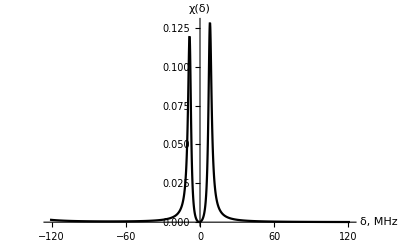

```mathematica
Plot[{Evaluate[Evaluate[Im[χpolmg0[[1]][[10]]]]/.{Δc->0,ω->0}]},{Δp,-20γ,20γ},AxesOrigin->{0,0},PlotStyle->Black,PlotRange->All,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]
```

```mathematica
mg1=1;
MatrixForm[sys3={{Subscript[ρ, g3g3],Subscript[ρ, g3s4],Subscript[ρ, g3e4],Subscript[ρ, g3e5]},{Subscript[ρ, s4g3],Subscript[ρ, s4s4],Subscript[ρ, s4e4],Subscript[ρ, s4e5]},{Subscript[ρ, e4g3],Subscript[ρ, e4s4],Subscript[ρ, e4e4],Subscript[ρ, e4e5]},{Subscript[ρ, e5g3],Subscript[ρ, e5s4],Subscript[ρ, e5e4],Subscript[ρ, e5e5]}}];
MatrixForm[h7={{0,0,Subscript[ΩP, g3e4],0},{0,-Δc+Δp,Subscript[ΩC, s4e4],Subscript[ΩC, s4e5]},{Subscript[ΩP, g3e4],Subscript[ΩC, s4e4],+Δp,0},{0,Subscript[ΩC, s4e5],0,hpf32+Δp}}]
TableForm[dt1={{0,0,0,0},{0,γsg,0,0},{0,0,γ/2,0},{0,0,0,γ/2}}];
TableForm[leqs3=(I*(h7.sys3-sys3.h7))+dt1.sys3]
solg3=Solve[{leqs3[[2,1]]==-I*ω*Subscript[ρ, s4g3],leqs3[[3,1]]==-I*ω*Subscript[ρ, e4g3],leqs3[[4,1]]==-I*ω*Subscript[ρ, e5g3],Subscript[χ, g4l]==-(Subscript[ΩP, g3e4]*Subscript[ρ, e4g3])},{Subscript[ρ, s4g3],Subscript[ρ, e4g3],Subscript[ρ, e5g3],Subscript[χ, g4l]}]/.{Subscript[ρ, s4e4]->0,Subscript[ρ, e4e4]->0,Subscript[ρ, e5s4]->0,Subscript[ρ, e5e4]->0,Subscript[ρ, g3g3]->1/3};
Subscript[χ, polm1]=Chop@Subscript[χ, g4l]/.solg3/.{Subscript[ΩP, g3e4]->Vp[Fe2,mg1+1,Fg,mg1],Subscript[ΩC, s4e4]->Vc[Fe2,mg1+1,Fs,mg1],Subscript[ΩC, s4e5]->Vc[Fe3,mg1+1,Fs,mg1]};
```

(0 | 0 | ΩP_g3e4 | 0
0 | -Δc+Δp | ΩC_s4e4 | ΩC_s4e5
ΩP_g3e4 | ΩC_s4e4 | Δp | 0
0 | ΩC_s4e5 | 0 | 266.65+Δp)

ⅈ (ρ_e4g3 ΩP_g3e4-ρ_g3e4 ΩP_g3e4) | ⅈ (-((-Δc+Δp) ρ_g3s4)-ρ_g3e4 ΩC_s4e4-ρ_g3e5 ΩC_s4e5+ρ_e4s4 ΩP_g3e4) | ⅈ (-Δp ρ_g3e4-ρ_g3s4 ΩC_s4e4+ρ_e4e4 ΩP_g3e4-ρ_g3g3 ΩP_g3e4) | ⅈ (-((266.65+Δp) ρ_g3e5)-ρ_g3s4 ΩC_s4e5+ρ_e4e5 ΩP_g3e4)
0.006065 ρ_s4g3+ⅈ ((-Δc+Δp) ρ_s4g3+ρ_e4g3 ΩC_s4e4+ρ_e5g3 ΩC_s4e5-ρ_s4e4 ΩP_g3e4) | 0.006065 ρ_s4s4+ⅈ (ρ_e4s4 ΩC_s4e4-ρ_s4e4 ΩC_s4e4+ρ_e5s4 ΩC_s4e5-ρ_s4e5 ΩC_s4e5) | 0.006065 ρ_s4e4+ⅈ (-Δp ρ_s4e4+(-Δc+Δp) ρ_s4e4+ρ_e4e4 ΩC_s4e4-ρ_s4s4 ΩC_s4e4+ρ_e5e4 ΩC_s4e5-ρ_s4g3 ΩP_g3e4) | 0.006065 ρ_s4e5+ⅈ (-((266.65+Δp) ρ_s4e5)+(-Δc+Δp) ρ_s4e5+ρ_e4e5 ΩC_s4e4+ρ_e5e5 ΩC_s4e5-ρ_s4s4 ΩC_s4e5)
3.0325 ρ_e4g3+ⅈ (Δp ρ_e4g3+ρ_s4g3 ΩC_s4e4-ρ_e4e4 ΩP_g3e4+ρ_g3g3 ΩP_g3e4) | 3.0325 ρ_e4s4+ⅈ (Δp ρ_e4s4-(-Δc+Δp) ρ_e4s4-ρ_e4e4 ΩC_s4e4+ρ_s4s4 ΩC_s4e4-ρ_e4e5 ΩC_s4e5+ρ_g3s4 ΩP_g3e4) | 3.0325 ρ_e4e4+ⅈ (-ρ_e4s4 ΩC_s4e4+ρ_s4e4 ΩC_s4e4-ρ_e4g3 ΩP_g3e4+ρ_g3e4 ΩP_g3e4) | 3.0325 ρ_e4e5+ⅈ (Δp ρ_e4e5-(266.65+Δp) ρ_e4e5+ρ_s4e5 ΩC_s4e4-ρ_e4s4 ΩC_s4e5+ρ_g3e5 ΩP_g3e4)
3.0325 ρ_e5g3+ⅈ ((266.65+Δp) ρ_e5g3+ρ_s4g3 ΩC_s4e5-ρ_e5e4 ΩP_g3e4) | 3.0325 ρ_e5s4+ⅈ ((266.65+Δp) ρ_e5s4-(-Δc+Δp) ρ_e5s4-ρ_e5e4 ΩC_s4e4-ρ_e5e5 ΩC_s4e5+ρ_s4s4 ΩC_s4e5) | 3.0325 ρ_e5e4+ⅈ (-Δp ρ_e5e4+(266.65+Δp) ρ_e5e4-ρ_e5s4 ΩC_s4e4+ρ_s4e4 ΩC_s4e5-ρ_e5g3 ΩP_g3e4) | 3.0325 ρ_e5e5+ⅈ (-ρ_e5s4 ΩC_s4e5+ρ_s4e5 ΩC_s4e5)

```mathematica
OD[[230]]
```

458.

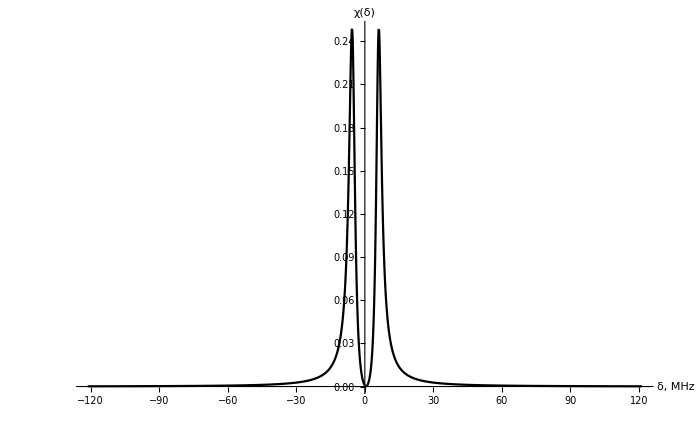

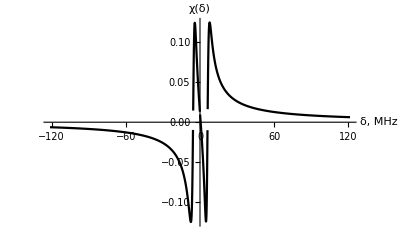

```mathematica
Plot[{Evaluate[Evaluate[Im[Subscript[χ, polm1][[1]][[18]]]]/.{Δc->0,ω->0}]},{Δp,-20γ,20γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]
Plot[{Evaluate[Evaluate[Re[Subscript[χ, polm1][[1]][[18]]]]/.{Δc->0,ω->0}]},{Δp,-20γ,20γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]
```

## We plot the transmission at a optical depth of OD=330

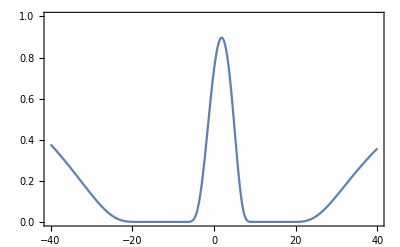

```mathematica
trans=Plot[Exp[-(γ/2*3*OD[[67]]/((∑_(m=-1)^1 Vp[Fe2,m+1,Fg,m]^2)))*Evaluate[Im[((χpolmgm1[[1]][[67]]/.{Δc->0,ω->0})+(χpolmg0[[1]][[67]]/.{Δc->0,ω->0})+(Subscript[χ, polm1][[1]][[67]]/.{Δc->0,ω->0}))]]],{Δp,-40,40},PlotRange->{0,1.0},Frame->True]
```

## Similarly that in the previous case, we create a table called “detfm” with the Δp’s where the transmission is maximum for every optical depth

```mathematica
detfm=Table[Δp/.Last[FindMaximum[{Exp[-(γ/2*3*OD[[i]]/((∑_(m=-1)^1 Vp[Fe2,m+1,Fg,m]^2)))*Evaluate[Im[(χpolmgm1[[1]][[i]]/.{Δc->0,ω->0})+(χpolmg0[[1]][[i]]/.{Δc->0,ω->0})+(Subscript[χ, polm1][[1]][[i]]/.{Δc->0,ω->0})]]],0<=Δp<=20},{Δp,1}]],{i,1,L001}];
```

## We follow the same procedure that before for the memory efficiency, i.e. by analyzing frequency domain and numerical Fourier transform. By integrating in frequency ω-domain

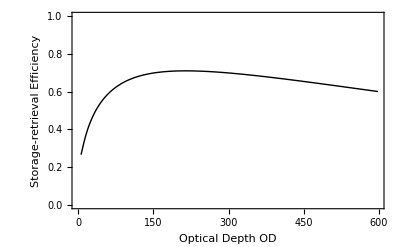

```mathematica
Wp0[ω_]:=(Tp/(√(4*Log[2])))Exp[(-ω^2 Tp^2)/(8*Log[2])];ϵω=Table[Wp0[ω]*Exp[-((γ/4)*3*OD[[i]]/((∑_(m=-1)^1 Vp[Fe2,m+1,Fg,m]^2)))*Evaluate[Im[(χpolmgm1[[1]][[i]]/.{Δc->0,Δp->detfm[[i]]})+(χpolmg0[[1]][[i]]/.{Δc->0,Δp->detfm[[i]]})+(Subscript[χ, polm1][[1]][[i]]/.{Δc->0,Δp->detfm[[i]]})]]],{i,1,L001}];
ηω=Table[NIntegrate[Abs[ϵω[[i]]]^2,{ω,-∞,∞}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1L001}];
ListPlot[Delete[Transpose@{OD,ηω},{{1},{2},{3}}],Frame->True,Joined->True,PlotRange->{All,{0,1}},PlotStyle->{Black,Thick},FrameLabel->{"Optical Depth OD","Storage-retrieval Efficiency"}]
```

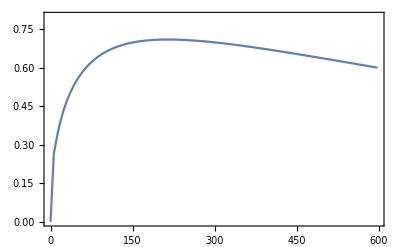

```mathematica
ListPlot[Insert[Delete[Transpose@{OD,ηω},{{1},{2},{3}}],{0,0},1],Joined->True,Frame->True,PlotRangePadding->None,PlotRange->{All,{0,0.8}}]
```

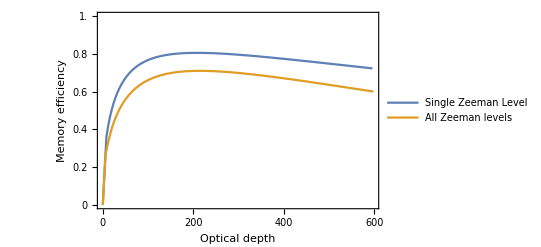

```mathematica
ListPlot[{Insert[Delete[data4l,{{1},{2}}],{0,0},1],Insert[Delete[Transpose@{OD,ηω},{{1},{2},{3}}],{0,0},1]},Joined->True,Frame->True,PlotRangePadding->None,PlotRange->{All,{0,1.0}},FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0},Automatic},{{0,100,200,300,400,500,600},None}},FrameLabel->{"Optical depth ","Memory efficiency"},PlotLegends->Placed[{"Single Zeeman Level","All Zeeman levels"},{0.75,0.25}]]
```

## By performing a complete numerical Fourier transform but with limits on time domain ranging from -6 to 6

```mathematica
ftallm=Table[Chop@NInverseFourierTransform[ϵω[[h]],ω,i],{h,2,L001},{i,-6,6,.25}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {-2.74411}. NIntegrate obtained -2.53838×10^-10+2.75032×10^-10 ⅈ and 4.25492×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {-2.74411}. NIntegrate obtained -2.53838×10^-10-2.75032×10^-10 ⅈ and 4.25492×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {-2.74411}. NIntegrate obtained -2.86466×10^-10+1.83099×10^-10 ⅈ and 3.91987×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.00434293+0.000301789 ⅈ,0.00555991+0.000312961 ⅈ,0.00705927+0.000314682 ⅈ,0.00889+0.000304276 ⅈ,0.0111042+0.00027931 ⅈ,0.0137557+0.0002378 ⅈ,0.0169+0.000178114 ⅈ,0.0205954+0.0000983992 ⅈ,0.0249061-4.35367×10^-6 ⅈ,0.0299047-0.000134895 ⅈ,0.0356666-0.000298558 ⅈ,0.0422455-0.000496796 ⅈ,0.0496217-0.000719205 ⅈ,0.0576332-0.000935641 ⅈ,0.0659468-0.00109776 ⅈ,0.0741952-0.00116293 ⅈ,18,0.0659468+0.00109776 ⅈ,0.0576332+0.000935641 ⅈ,0.0496217+0.000719205 ⅈ,0.0422455+0.000496796 ⅈ,0.0356666+0.000298558 ⅈ,0.0299047+0.000134895 ⅈ,0.0249061+4.35367×10^-6 ⅈ,0.0205954-0.0000983992 ⅈ,0.0169-0.000178114 ⅈ,0.0137557-0.0002378 ⅈ,0.0111042-0.00027931 ⅈ,0.00889-0.000304276 ⅈ,0.00705927-0.000314682 ⅈ,0.00555991-0.000312961 ⅈ,0.00434293-0.000301789 ⅈ},197,{0,0,0,43,0,0,0}}
 |  |  |  |

```mathematica
τ=Table[τ=tim;τ,{tim,-6,6,0.25}];
Transpose@{OD,Chop@Table[NIntegrate[(Interpolation[Transpose@{τ,ftallm[[i]]},InterpolationOrder->3][t])^2,{t,-6,6}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,Length[ftallm]}]}
ListPlot[Transpose@{OD,Chop@Table[NIntegrate[(Interpolation[Transpose@{τ,ftallm[[i]]},InterpolationOrder->3][t])^2,{t,-6,6}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,Length[ftallm]}]},Joined->True,PlotRange->{0,0.5},Frame->True]
```

## Finally, we plot in the same frame the three lines obtained. We observe that with the Taylor expansion, we get a higher curve. By comparing with the correct line of your work, we have a lower curve; it does not achieve the correct maximum (around 0.67).

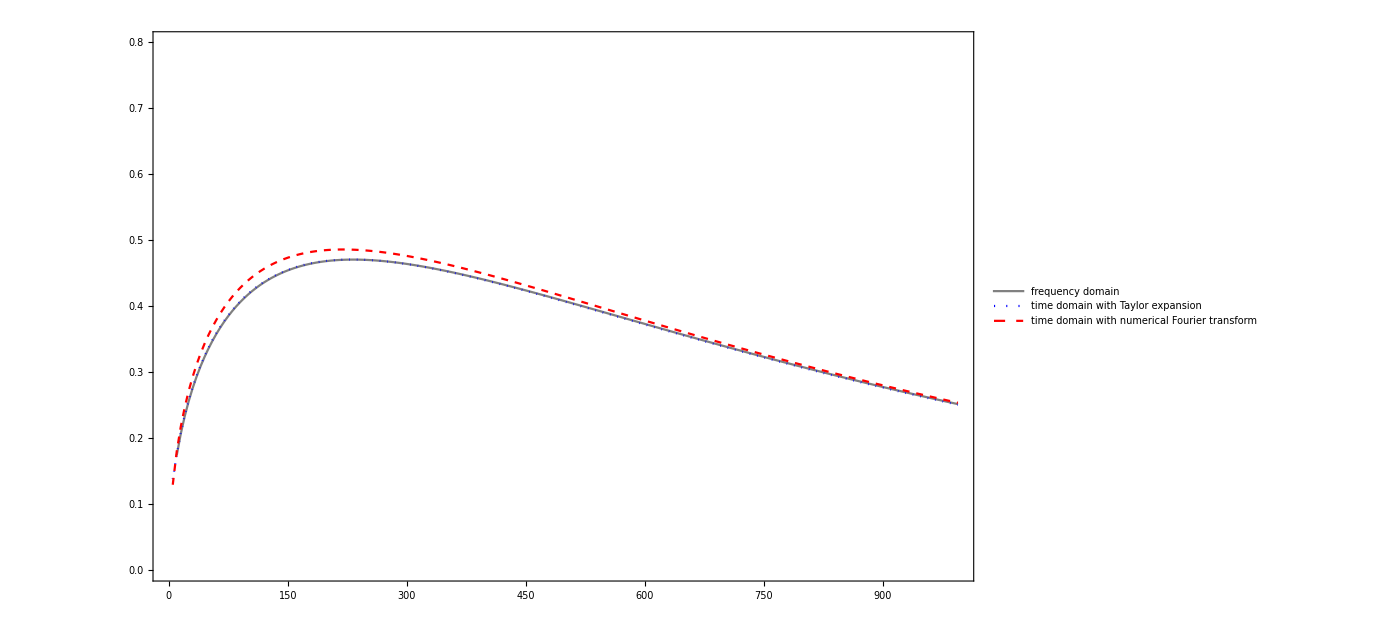

```mathematica
ListPlot[{Delete[Transpose@{OD,ηω},{{1},{2}}],Transpose@{Delete[OD,{{1}}],Chop@Table[NIntegrate[(Interpolation[Transpose@{τ,ftallm[[i]]},InterpolationOrder->3][t])^2,{t,-6,6}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,Length[ftallm]}]},Delete[Transpose@{OD,effd2},{{1}}]},Joined->True,PlotRange->{0,0.8},Frame->True,PlotStyle->{Gray,{Blue,Dotted},{Red,Dashed}},FrameTicksStyle->Directive[Black,18],PlotLegends->Placed[{"frequency domain","time domain with numerical Fourier transform","time domain with Taylor expansion"},{0.55,0.3}]]
```

# We analyze the Rubidium 87 D1 - Line

```mathematica
(*Parameters and dipole moments of the probe pulse*)

Fg=1;
Fs=2;
Fe1=1;
Fe2=2;
S=1/2;
IS=3/2;
j=1/2;
Tp=0.500;
ζ=2.0;
γ=5.7;
Γ=5.7;
γsg=0.001*γ;
hbar=1;
hpf12=816.65;
OD=Table[OD=od ;OD,{od,0.00001,600.0,5}];
L001=Length[OD];
Rabi=√((OD*γ)/(ζ*Tp)) ;
```

```mathematica
Vp[Fe_,me_,Fg_,mg_]:=√(3/4*hbar*(2*j+1)*(2*Fg+1))*ClebschGordan[{Fg,mg},{1,me-mg},{Fe,me}]*SixJSymbol[{S,IS,Fg},{Fe,1,j}]*√γ;

Vc[Fe_,me_,Fs_,ms_]:=((ClebschGordan[{Fs,ms},{1,me-ms},{Fe,me}]*SixJSymbol[{S,IS,Fs},{Fe,1,j}])/(ClebschGordan[{2,-1},{1,1},{2,0}]*SixJSymbol[{S,IS,Fs},{2,1,j}]))*Rabi/2;
```

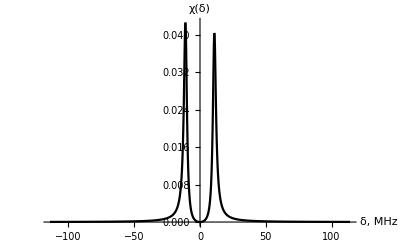

```mathematica
mgm1=-1;
MatrixForm[sysm1={{Subscript[ρ, gm1gm1],Subscript[ρ, gm1sm1],Subscript[ρ, gm1e30],Subscript[ρ, gm1e40]},{Subscript[ρ, sm1gm1],Subscript[ρ, sm1sm1],Subscript[ρ, sm1e30],Subscript[ρ, sm1e40]},{Subscript[ρ, e30gm1],Subscript[ρ, e30sm1],Subscript[ρ, e30e30],Subscript[ρ, e30e40]},{Subscript[ρ, e40gm1],Subscript[ρ, e40sm1],Subscript[ρ, e40e30],Subscript[ρ, e40e40]}}];
Clear[h3];
MatrixForm[h3={{0,0,Subscript[ΩP, gm1e30],Subscript[ΩP, gm1e40]},{0,Δc-Δp,Subscript[ΩC, sm1e30],Subscript[ΩC, sm1e40]},{Subscript[ΩP, gm1e30],Subscript[ΩC, sm1e30],hpf12-Δp,0},{Subscript[ΩP, gm1e40],Subscript[ΩC, sm1e40],0,-Δp}}];
TableForm[dt1={{0,0,0,0},{0,γsg,0,0},{0,0,γ/2,0},{0,0,0,γ/2}}];
TableForm[leqsm1=(I*(h3.sysm1-sysm1.h3))+dt1.sysm1];
solgm1=Solve[{leqsm1[[2,1]]==-I*ω*Subscript[ρ, sm1gm1],leqsm1[[3,1]]==-I*ω*Subscript[ρ, e30gm1],leqsm1[[4,1]]==-I*ω*Subscript[ρ, e40gm1],Subscript[χ, gm1]==-(Subscript[ΩP, gm1e40]*Subscript[ρ, e40gm1]+Subscript[ΩP, gm1e30]*Subscript[ρ, e30gm1])},{Subscript[ρ, sm1gm1],Subscript[ρ, e40gm1],Subscript[ρ, e30gm1],Subscript[χ, gm1]}]/.{Subscript[ρ, e30e30]->0,Subscript[ρ, sm1e30]->0,Subscript[ρ, sm1e40]->0,Subscript[ρ, e30e40]->0,Subscript[ρ, e40e30]->0,Subscript[ρ, e40e40]->0,Subscript[ρ, gm1gm1]->1/3};
Subscript[χ, gm1pol]=Chop@Subscript[χ, gm1]/.solgm1/.{Subscript[ΩP, gm1e30]->Vp[Fe1,mgm1+1,Fg,mgm1],Subscript[ΩP, gm1e40]->Vp[Fe2,mgm1+1,Fg,mgm1],Subscript[ΩC, sm1e30]->Vc[Fe1,mgm1+1,Fs,mgm1],Subscript[ΩC, sm1e40]->Vc[Fe2,mgm1+1,Fs,mgm1]};
Plot[{Evaluate[Evaluate[Im[Subscript[χ, gm1pol][[1]][[18]]]]/.{Δc->0,ω->0}]},{Δp,-20γ,20γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]
```

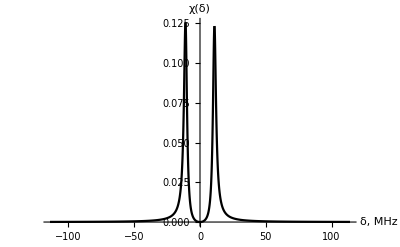

```mathematica
mg=0;
MatrixForm[sys0={{Subscript[ρ, g0g0],Subscript[ρ, g0s0],Subscript[ρ, g0e30],Subscript[ρ, g0e40]},{Subscript[ρ, s0g0],Subscript[ρ, s0s0],Subscript[ρ, s0e31],Subscript[ρ, s0e31]},{Subscript[ρ, e31g0],Subscript[ρ, e31s0],Subscript[ρ, e31e31],Subscript[ρ, e31e41]},{Subscript[ρ, e41g0],Subscript[ρ, e41s0],Subscript[ρ, e41e31],Subscript[ρ, e41e41]}}];
MatrixForm[h4={{0,0,Subscript[ΩP, g0e31],Subscript[ΩP, g0e41]},{0,Δc-Δp,Subscript[ΩC, s0e31],Subscript[ΩC, s0e41]},{Subscript[ΩP, g0e31],Subscript[ΩC, s0e31],hpf12-Δp,0},{Subscript[ΩP, g0e41],Subscript[ΩC, s0e41],0,-Δp}}];
TableForm[dt1={{0,0,0,0},{0,γsg,0,0},{0,0,γ/2,0},{0,0,0,γ/2}}];
TableForm[leqs0=(I*(h4.sys0-sys0.h4))+dt1.sys0];
solg0=Solve[{leqs0[[2,1]]==-I*ω*Subscript[ρ, s0g0],leqs0[[3,1]]==-I*ω*Subscript[ρ, e31g0],leqs0[[4,1]]==-I*ω*Subscript[ρ, e41g0],Subscript[χ, g0]==-(Subscript[ΩP, g0e31]*Subscript[ρ, e31g0]+Subscript[ΩP, g0e41]*Subscript[ρ, e41g0])},{Subscript[ρ, s0g0],Subscript[ρ, e41g0],Subscript[ρ, e31g0],Subscript[χ, g0]}]/.{Subscript[ρ, e31e31]->0,Subscript[ρ, s0e31]->0,Subscript[ρ, s0e41]->0,Subscript[ρ, e31e41]->0,Subscript[ρ, e41e31]->0,Subscript[ρ, e41e41]->0,Subscript[ρ, g0g0]->1/3};
Subscript[χ, g0pol]=Chop@Subscript[χ, g0]/.solg0/.{Subscript[ΩP, g0e31]->Vp[Fe1,mg+1,Fg,mg],Subscript[ΩP, g0e41]->Vp[Fe2,mg+1,Fg,mg],Subscript[ΩC, s0e31]->Vc[Fe1,mg+1,Fs,mg],Subscript[ΩC, s0e41]->Vc[Fe2,mg+1,Fs,mg]};
Plot[{Evaluate[Evaluate[Im[Subscript[χ, g0pol][[1]][[18]]]]/.{Δc->0,ω->0}]},{Δp,-20γ,20γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]
```

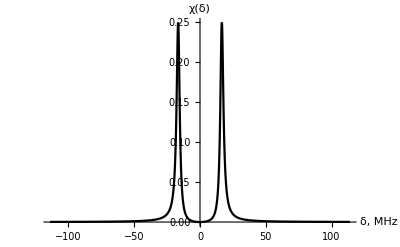

```mathematica
mg1=1;
MatrixForm[sys1={{Subscript[ρ, g3g3],Subscript[ρ, g3s3],Subscript[ρ, g3e44]},{Subscript[ρ, s3g3],Subscript[ρ, s3s3],Subscript[ρ, s3e44]},{Subscript[ρ, e44g3],Subscript[ρ, e44s3],Subscript[ρ, e44e44]}}];
MatrixForm[h7={{0,0,Subscript[ΩP, g3e44]},{0,Δc-Δp,Subscript[ΩC, s3e44]},{Subscript[ΩP, g3e44],Subscript[ΩC, s3e44],-Δp}}];
TableForm[dt1={{0,0,0},{0,γsg,0},{0,0,γ/2}}];
TableForm[leqs3=(I*(h7.sys1-sys1.h7))+dt1.sys1];
solg3=Solve[{leqs3[[2,1]]==-I*ω*Subscript[ρ, s3g3],leqs3[[3,1]]==-I*ω*Subscript[ρ, e44g3],Subscript[χ, g3]==-(Subscript[ΩP, g3e44]*Subscript[ρ, e44g3])},{Subscript[ρ, s3g3],Subscript[ρ, e44g3],Subscript[χ, g3]}]/.{Subscript[ρ, e44e44]->0,Subscript[ρ, s3e44]->0,Subscript[ρ, g3g3]->1/3};
Subscript[χ, g1pol]=Chop@Subscript[χ, g3]/.solg3/.{Subscript[ΩP, g3e44]->Vp[Fe2,mg1+1,Fg,mg1],Subscript[ΩC, s3e44]->Vc[Fe2,mg1+1,Fs,mg1]};
Plot[{Evaluate[Evaluate[Im[Subscript[χ, g1pol][[1]][[59]]]]/.{Δc->0,ω->0}]},{Δp,-20γ,20γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]
```

## Transmission and efficiency with all Zeeman sublevels

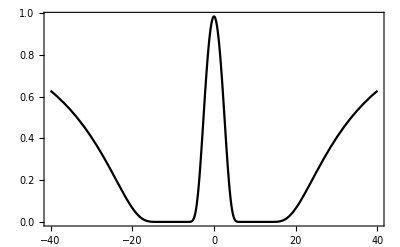

```mathematica
Plot[Exp[-((γ/2)*3*OD[[17]]/((∑_(m=-1)^1 Vp[Fe2,m+1,Fg,m]^2)))*Evaluate[Im[(Subscript[χ, gm1pol][[1]][[17]]/.{Δc->0,ω->0})+(Subscript[χ, g0pol][[1]][[17]]/.{Δc->0,ω->0})+(Subscript[χ, g1pol][[1]][[17]]/.{Δc->0,ω->0})]]],{Δp,-40,40},PlotStyle->Black,Frame->True,PlotRange->All]
```

```mathematica
detd1=Table[Δp/.Last[FindMaximum[{Exp[-((γ/2)*3*OD[[i]]/((∑_(m=-1)^1 Vp[Fe2,m+1,Fg,m]^2)))*Evaluate[Im[(Subscript[χ, gm1pol][[1]][[i]]/.{Δc->0,ω->0})+(Subscript[χ, g0pol][[1]][[i]]/.{Δc->0,ω->0})+(Subscript[χ, g1pol][[1]][[i]]/.{Δc->0,ω->0})]]],-4<=Δp<=0},{Δp,-1}]],{i,1,L001}]
```

{-3.73338,-0.000362282,-0.000576892,-0.00076324,-0.000863611,-0.000945674,-0.00101632,-0.00107868,-0.0011348,-0.00106871,-0.00110744,-0.00114316,-0.00117643,-0.00120768,-0.00123721,-0.00231597,-0.00236951,-0.00242743,-0.0024812,-0.00253197,-0.00258037,-0.00262682,-0.00267158,-0.00271486,-0.00275682,-0.00279758,-0.00283725,-0.00287591,-0.00291364,-0.0029505,-0.00298656,-0.00302185,-0.00305643,-0.00309034,-0.0031236,-0.00298098,-0.00300977,-0.00303805,-0.00306584,-0.00309316,-0.00312003,-0.00314647,-0.00317249,-0.00319813,-0.00322338,-0.00324826,-0.00327279,-0.00329698,-0.00332084,-0.00334438,-0.00336762,-0.00339056,-0.00341322,-0.00343562,-0.00325098,-0.00327023,-0.00328924,-0.00330802,-0.00332656,-0.0033449,-0.00336301,-0.00338092,-0.00339863,-0.00341614,-0.00343346,-0.00345059,-0.00346754,-0.00348431,-0.00350091,-0.00351734,-0.0035336,-0.0035497,-0.00356565,-0.00358144,-0.00359708,-0.00361258,-0.00362794,-0.00364316,-0.00365823,-0.00367317,-0.00368798,-0.00370266,-0.00371722,-0.00373165,-0.00374597,-0.00376017,-0.00377424,-0.00378821,-0.00380207,-0.00381581,-0.00382946,-0.00384299,-0.00385642,-0.00386976,-0.00388299,-0.00389612,-0.00390916,-0.00392211,-0.00393496,-0.00394772,-0.00369036,-0.00370102,-0.0037116,-0.0037221,-0.00373253,-0.00374288,-0.00375315,-0.00376335,-0.00377348,-0.00378353,-0.00379352,-0.00380343,-0.00381328,-0.00382306,-0.00383277,-0.00384243,-0.00385201,-0.00386153,-0.003871,-0.00388039}

## We follow the same procedure that before for the memory efficiency, i . e . by analyzing frequency domain, Taylor expansion in ω for integrating in time domain, and numerical Fourier transform . By integrating in frequency ω - domain

```mathematica
Wp0[ω_]:=Tp/(√(4*Log[2]))Exp[(-ω^2 Tp^2)/(8*Log[2])];
ϵd1out=Table[Wp0[ω]*Exp[(γ/4*3*OD[[i]]/(∑_(m=-1)^1 Vp[Fe2,m+1,Fg,m]^2))*Evaluate[I*((Subscript[χ, gm1pol][[1]][[i]]/.{Δc->0,Δp->0})+(Subscript[χ, g0pol][[1]][[i]]/.{Δc->0,Δp->0})+(Subscript[χ, g1pol][[1]][[i]]/.{Δc->0,Δp->0}))]],{i,1,L001}];
```

{{10.,0.31172},{15.,0.365286},{20.,0.409988},{25.,0.447832},{30.,0.480518},{35.,0.50919},{40.,0.534641},{45.,0.557444},{50.,0.578029},{55.,0.596727},{60.,0.613802},{65.,0.629466},{70.,0.643892},{75.,0.657225},{80.,0.669587},{85.,0.681083},{90.,0.691799},{95.,0.701814},{100.,0.711192},{105.,0.719994},{110.,0.73108},{115.,0.736064},{120.,0.743418},{125.,0.750367},{130.,0.756943},{135.,0.763174},{140.,0.769088},{145.,0.774705},{150.,0.780049},{155.,0.785138},{160.,0.789989},{165.,0.794619},{170.,0.799042},{175.,0.803271},{180.,0.807318},{185.,0.811194},{190.,0.814911},{195.,0.818476},{200.,0.8219},{205.,0.825191},{210.,0.828354},{215.,0.831399},{220.,0.834331},{225.,0.837156},{230.,0.83988},{235.,0.842508},{240.,0.845045},{245.,0.847495},{250.,0.849863},{255.,0.852153},{260.,0.854369},{265.,0.856513},{270.,0.85859},{275.,0.860602},{280.,0.862553},{285.,0.864444},{290.,0.866279},{295.,0.868061},{300.,0.869791},{305.,0.871471},{310.,0.873104},{315.,0.874691},{320.,0.876235},{325.,0.877737},{330.,0.879199},{335.,0.880622},{340.,0.882008},{345.,0.883359},{350.,0.884675},{355.,0.885958},{360.,0.887209},{365.,0.888429},{370.,0.88962},{375.,0.890782},{380.,0.891917},{385.,0.893025},{390.,0.894107},{395.,0.895165},{400.,0.896198},{405.,0.897209},{410.,0.898197},{415.,0.899163},{420.,0.900108},{425.,0.901033},{430.,0.901938},{435.,0.902825},{440.,0.903693},{445.,0.904542},{450.,0.905375},{455.,0.906191},{460.,0.90699},{465.,0.907773},{470.,0.908541},{475.,0.909295},{480.,0.910033},{485.,0.910758},{490.,0.911468},{495.,0.912166},{500.,0.91285},{505.,0.913522},{510.,0.914182},{515.,0.91483},{520.,0.915466},{525.,0.916091},{530.,0.916704},{535.,0.917308},{540.,0.9179},{545.,0.918483},{550.,0.919055},{555.,0.919618},{560.,0.920172},{565.,0.920716},{570.,0.921251},{575.,0.921778},{580.,0.922296},{585.,0.922805},{590.,0.923307},{595.,0.9238}}

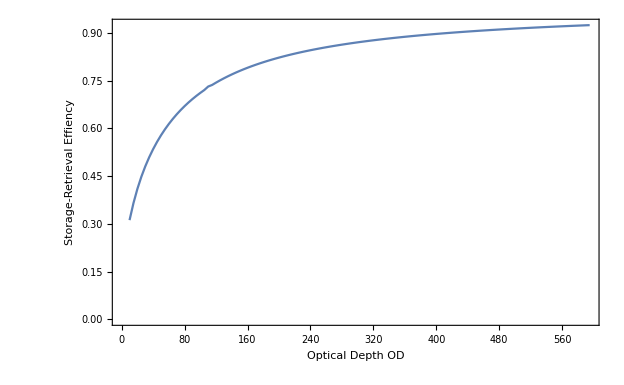

```mathematica
effd1c=Table[NIntegrate[Abs[ϵd1out[[i]]]^2,{ω,-∞,∞}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,L001}];
Delete[Transpose@{OD,effd1c},{{1},{2}}]
ListPlot[Delete[Transpose@{OD,effd1c},{{1},{2}}],Joined->True,Frame->True,FrameLabel->{"Optical Depth OD","Storage-Retrieval Effiency",PlotRange->{0,1.5}},FrameTicksStyle->Directive[Black,12]]
```

## Numerical Fourier Transform function throught Mathematica function NInverseFourier transform. We have to run the first line of the code. The time interval where we calculate the Fourier transform (thus the efficiency) is from -6 to 6, in steps size of 0.25.

```mathematica
τ=Table[τ=tim;τ,{tim,-6,6,0.25}];
OD=Table[OD=od ;OD,{od,0.00001,600,5}];
Wp0[ω_]:=(Tp/(√(4Log[2])))*Exp[(-ω^2 Tp^2)/(8*Log[2])];
L001=Length[OD];

ϵd1out=Table[Wp0[ω]*Exp[(γ/4*3*OD[[i]]/(∑_(m=-1)^1 Vp[Fe2,m+1,Fg,m]^2))*Evaluate[I*((Subscript[χ, gm1pol][[1]][[i]]/.{Δc->0,Δp->0})+(Subscript[χ, g0pol][[1]][[i]]/.{Δc->0,Δp->0})+(Subscript[χ, g1pol][[1]][[i]]/.{Δc->0,Δp->0}))]],{i,1,L001}];
```

```mathematica
ftd1=Table[Chop@NInverseFourierTransform[ϵd1out[[h]],ω,i,AccuracyGoal->9],{h,2,L001},{i,-6,6,.25}];
Chop@Table[NIntegrate[Abs[Interpolation[Transpose@{τ,ftd1[[i]]},InterpolationOrder->3][t]]^2,{t,-5,5}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,Length[ftd1]}]
```

{0.259798,0.311425,0.365184,0.409882,0.447689,0.480316,0.508919,0.534344,0.557018,0.577514,0.596117,0.613094,0.628656,0.642978,0.656205,0.668459,0.679845,0.690452,0.700357,0.709626,0.718318,0.726485,0.734172,0.741419,0.748263,0.754735,0.760864,0.766676,0.772195,0.777442,0.782435,0.787192,0.79173,0.796063,0.800203,0.804164,0.807955,0.811589,0.815074,0.818418,0.821631,0.824719,0.827689,0.830548,0.833303,0.835957,0.838517,0.840988,0.843373,0.845678,0.847906,0.850061,0.852146,0.854165,0.85612,0.858015,0.859852,0.861635,0.863364,0.865043,0.866673,0.868257,0.869797,0.871294,0.872751,0.874168,0.875547,0.87689,0.878199,0.879473,0.880716,0.881927,0.883109,0.884262,0.885386,0.886484,0.887557,0.888604,0.889627,0.890626,0.891603,0.892559,0.893493,0.894407,0.895301,0.896176,0.897032,0.897871,0.898692,0.899496,0.900284,0.901056,0.901813,0.902554,0.903282,0.903995,0.904694,0.90538,0.906053,0.906714,0.907363,0.907999,0.908624,0.909238,0.909841,0.910433,0.911015,0.911586,0.912148,0.9127,0.913243,0.913777,0.914302,0.914818,0.915325,0.915825,0.916316,0.916799,0.917275}

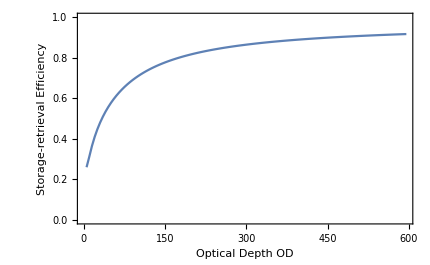

```mathematica
ListPlot[Transpose@{Delete[OD,{{1}}],Chop@Table[NIntegrate[Abs[Interpolation[Transpose@{τ,ftd1[[i]]},InterpolationOrder->3][t]]^2,{t,-6,6}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,Length[ftd1]}]},Joined->True,PlotRange->{0,1.0},Frame->True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"Optical Depth OD","Storage-retrieval Efficiency"}]
```

## We briefly verify the case with optical pumping to m=3, which is the case of an effective three-level scheme

```mathematica
(*Dipole moments of the probe pulse*)

Fg=3;
Fs=4;
Fe4=4;
Fe3=3;
S=1/2;
IS=7/2;
j=3/2;
Tp=0.500;
ζ=2.0;
γ=4.5612;
γsg=0.001*γ;
Γ=4.5612;
hbar=1;
hpf34=1167.680;
(*2.7*)

OD=Table[OD=od ;OD,{od,0.00001,600.0,5}];
L001=Length[OD];
Rabi=√((OD*γ)/(ζ*Tp)) ;
Vp[Fe_,me_,Fg_,mg_]:=√(3/4*hbar*(2*j+1)*(2*Fg+1))*ClebschGordan[{Fg,mg},{1,me-mg},{Fe,me}]*SixJSymbol[{S,IS,Fg},{Fe,1,j}]*√γ;

Vc[Fe_,me_,Fs_,ms_]:=((ClebschGordan[{Fs,ms},{1,me-ms},{Fe,me}]*SixJSymbol[{S,IS,Fs},{Fe,1,j}])/(ClebschGordan[{4,3},{1,1},{4,4}]*SixJSymbol[{S,IS,Fs},{4,1,j}]))*Rabi/2;
```

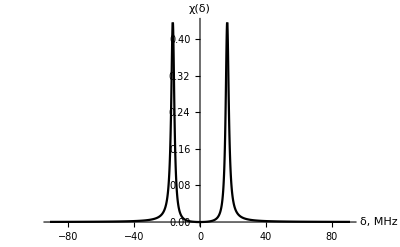

```mathematica
mg3=3;
MatrixForm[sys3={{Subscript[ρ, g3g3],Subscript[ρ, g3s3],Subscript[ρ, g3e44]},{Subscript[ρ, s3g3],Subscript[ρ, s3s3],Subscript[ρ, s3e44]},{Subscript[ρ, e44g3],Subscript[ρ, e44s3],Subscript[ρ, e44e44]}}];
MatrixForm[h7={{0,0,Subscript[ΩP, g3e44]},{0,Δc-Δp,Subscript[ΩC, s3e44]},{Subscript[ΩP, g3e44],Subscript[ΩC, s3e44],-Δp}}];
TableForm[dt1={{0,0,0},{0,γsg,0},{0,0,γ/2}}];
TableForm[leqs3=(I*(h7.sys3-sys3.h7))+dt1.sys3];
solg3=Solve[{leqs3[[2,1]]==-I*ω*Subscript[ρ, s3g3],leqs3[[3,1]]==-I*ω*Subscript[ρ, e44g3],Subscript[χ, g3]==-(Subscript[ρ, e44g3]/Subscript[ΩP, g3e44])},{Subscript[ρ, s3g3],Subscript[ρ, e44g3],Subscript[χ, g3]}]/.{Subscript[ρ, e44e44]->0,Subscript[ρ, s3e44]->0,Subscript[ρ, g3g3]->1};
Subscript[χ, g3l]=Chop@Subscript[χ, g3]/.solg3/.{Subscript[ΩP, g3e44]->Vp[Fe4,mg3+1,Fg,mg3],Subscript[ΩC, s3e44]->Vc[Fe4,mg3+1,Fs,mg3]};
Plot[{Evaluate[Evaluate[Im[Subscript[χ, g3l][[1]][[49]]]]/.{Δc->0,ω->0}]},{Δp,-20γ,20γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]
```

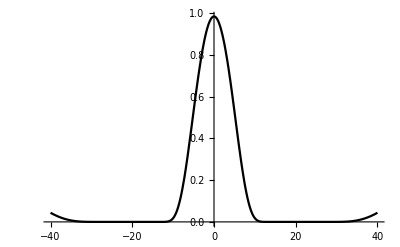

```mathematica
Plot[Exp[-((γ/2)*OD[[115]])*Evaluate[Im[(Subscript[χ, g3l][[1]][[115]]/.{Δc->0,ω->0})]]],{Δp,-40,40},PlotStyle->Black,PlotRange->All]
```

```mathematica
detd1l=Table[Δp/.Last[FindMaximum[{Exp[-((γ/2)*OD[[i]])*Evaluate[Im[(Subscript[χ, g3l][[1]][[i]]/.{Δc->0,ω->0})]]],-5<=Δp<=0},{Δp,-1}]],{i,1,L001}]
```

{-4.97721,-0.000550538,-0.000814145,-0.000964673,-0.00107974,-0.00117488,-0.00112405,-0.00118257,-0.00123506,-0.00234702,-0.00242275,-0.00250875,-0.00258738,-0.00266087,-0.00273037,-0.00279661,-0.00286007,-0.00292112,-0.00281394,-0.0028648,-0.00291405,-0.00296185,-0.0030083,-0.00305352,-0.00309761,-0.00314063,-0.00318266,-0.00302426,-0.00305952,-0.00309402,-0.00312778,-0.00316087,-0.0031933,-0.00322512,-0.00325635,-0.00328701,-0.00331714,-0.00334674,-0.00337586,-0.00340451,-0.0034327,-0.00346046,-0.0034878,-0.00351473,-0.00354127,-0.00356744,-0.00359324,-0.0036187,-0.00364381,-0.0036686,-0.00344126,-0.00346189,-0.00348225,-0.00350234,-0.00352217,-0.00354175,-0.00356107,-0.00358016,-0.00359902,-0.00361766,-0.00363607,-0.00365427,-0.00367226,-0.00369005,-0.00370765,-0.00372505,-0.00374226,-0.00375929,-0.00377616,-0.00379283,-0.00380935,-0.0038257,-0.00384188,-0.00385792,-0.00387379,-0.00388953,-0.0039051,-0.00392054,-0.00393583,-0.003951,-0.00396603,-0.00398092,-0.00399569,-0.00401033,-0.00402485,-0.00403925,-0.00405353,-0.00406769,-0.00408174,-0.00409569,-0.00410952,-0.00755953,-0.00758123,-0.00760274,-0.00762402,-0.00764516,-0.00766612,-0.00768687,-0.00770747,-0.00772789,-0.00774815,-0.00776827,-0.0077882,-0.00780799,-0.00782763,-0.00784711,-0.00786642,-0.00788562,-0.00790465,-0.00792357,-0.00794233,-0.00796093,-0.00797942,-0.0079978,-0.00801604,-0.00803413,-0.00805211,-0.00806998,-0.00808772,-0.00810533}

## We follow the same procedure that before for the memory efficiency, i . e . by analyzing frequency domain, Taylor expansion in ω for integrating in time domain, and numerical Fourier transform . By integrating in frequency ω - domain

{-4.97721,-0.000550538,-0.000814145,-0.000964673,-0.00107974,-0.00117488,-0.00112405,-0.00118257,-0.00123506,-0.00234702,-0.00242275,-0.00250875,-0.00258738,-0.00266087,-0.00273037,-0.00279661,-0.00286007,-0.00292112,-0.00281394,-0.0028648,-0.00291405,-0.00296185,-0.0030083,-0.00305352,-0.00309761,-0.00314063,-0.00318266,-0.00302426,-0.00305952,-0.00309402,-0.00312778,-0.00316087,-0.0031933,-0.00322512,-0.00325635,-0.00328701,-0.00331714,-0.00334674,-0.00337586,-0.00340451,-0.0034327,-0.00346046,-0.0034878,-0.00351473,-0.00354127,-0.00356744,-0.00359324,-0.0036187,-0.00364381,-0.0036686,-0.00344126,-0.00346189,-0.00348225,-0.00350234,-0.00352217,-0.00354175,-0.00356107,-0.00358016,-0.00359902,-0.00361766,-0.00363607,-0.00365427,-0.00367226,-0.00369005,-0.00370765,-0.00372505,-0.00374226,-0.00375929,-0.00377616,-0.00379283,-0.00380935,-0.0038257,-0.00384188,-0.00385792,-0.00387379,-0.00388953,-0.0039051,-0.00392054,-0.00393583,-0.003951,-0.00396603,-0.00398092,-0.00399569,-0.00401033,-0.00402485,-0.00403925,-0.00405353,-0.00406769,-0.00408174,-0.00409569,-0.00410952,-0.00755953,-0.00758123,-0.00760274,-0.00762402,-0.00764516,-0.00766612,-0.00768687,-0.00770747,-0.00772789,-0.00774815,-0.00776827,-0.0077882,-0.00780799,-0.00782763,-0.00784711,-0.00786642,-0.00788562,-0.00790465,-0.00792357,-0.00794233,-0.00796093,-0.00797942,-0.0079978,-0.00801604,-0.00803413,-0.00805211,-0.00806998,-0.00808772,-0.00810533}

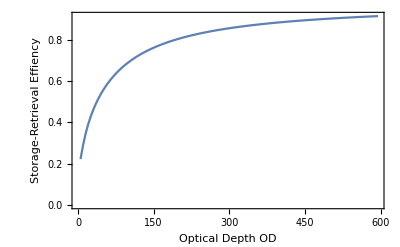

```mathematica
Wp0[ω_]:=Tp/(√(4*Log[2]))Exp[(-ω^2 Tp^2)/(8*Log[2])];
detd1l=Table[Δp/.Last[FindMaximum[{Exp[-((γ/2)*OD[[i]])*Evaluate[Im[(Subscript[χ, g3l][[1]][[i]]/.{Δc->0,ω->0})]]],-5<=Δp<=0},{Δp,-1}]],{i,1,L001}]
ϵd1lout=Table[Wp0[ω]*Exp[(γ/2*OD[[i]])*Evaluate[I*(Subscript[χ, g3l][[1]][[i]]/.{Δc->0,Δp->detd1l[[i]]})]],{i,1,L001}];
effd1l=Table[NIntegrate[Abs[ϵd1lout[[i]]]^2,{ω,-∞,∞}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,L001}];
ListPlot[Delete[Transpose@{OD,effd1l},{{1}}],Joined->True,Frame->True,FrameLabel->{"Optical Depth OD","Storage-Retrieval Effiency",PlotRange->{0,1}}]
```

## Numerical Fourier Transform function throught Mathematica function NInverseFourier transform. We have to run the first line of the code. The time interval where we calculate the Fourier transform (thus the efficiency) is from -6 to 6, in steps size of 0.25.

```mathematica
τ=Table[τ=tim;τ,{tim,-4,4,0.25}];
OD=Table[OD=od ;OD,{od,0.00001,600,5}];
Wp0[ω_]:=Tp/(√(4Log[2]))*Exp[(-ω^2 Tp^2)/(8*Log[2])];
L001=Length[OD];
detd1l=Table[Δp/.Last[FindMaximum[{Exp[-((γ/2)*OD[[i]])*Evaluate[Im[(Subscript[χ, g3l][[1]][[i]]/.{Δc->0,ω->0})]]],-5<=Δp<=0},{Δp,-1}]],{i,1,L001}];

ϵd1lout=Table[Wp0[ω]*Exp[(γ/2*OD[[i]])*Evaluate[I*(Subscript[χ, g3l][[1]][[i]]/.{Δc->0,Δp->detd1l[[i]]})]],{i,1,L001}];
```

```mathematica
ftd1l=Table[Chop@NInverseFourierTransform[ϵd1lout[[h]],ω,i,AccuracyGoal->9],{h,2,L001},{i,-4,4,.25}];
Chop@Table[NIntegrate[Abs[Interpolation[Transpose@{τ,ftd1l[[i]]},InterpolationOrder->3][t]]^2,{t,-4,4}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,Length[ftd1l]}]
```

{0.215226,0.287147,0.342723,0.386724,0.423762,0.456062,0.484754,0.510407,0.533445,0.554208,0.572998,0.590086,0.605714,0.620088,0.63338,0.64573,0.657251,0.668033,0.678149,0.687658,0.696609,0.705045,0.713003,0.720518,0.727621,0.734342,0.740707,0.746743,0.752473,0.75792,0.763105,0.768047,0.772763,0.777269,0.781581,0.78571,0.789669,0.793469,0.797119,0.800629,0.804006,0.807258,0.810391,0.813413,0.816327,0.819141,0.821858,0.824483,0.827021,0.829475,0.83185,0.834149,0.836375,0.838532,0.840623,0.84265,0.844617,0.846526,0.848379,0.850179,0.851928,0.853628,0.855282,0.85689,0.858456,0.85998,0.861464,0.86291,0.86432,0.865694,0.867034,0.868342,0.869617,0.870863,0.872079,0.873267,0.874427,0.875561,0.87667,0.877754,0.878814,0.879851,0.880865,0.881859,0.882831,0.883782,0.884714,0.885627,0.886522,0.887399,0.888257,0.889099,0.889925,0.890735,0.891529,0.892308,0.893073,0.893823,0.89456,0.895283,0.895993,0.89669,0.897375,0.898047,0.898708,0.899357,0.899995,0.900623,0.901239,0.901846,0.902442,0.903028,0.903605,0.904172,0.90473,0.905279,0.90582,0.906352,0.906875}

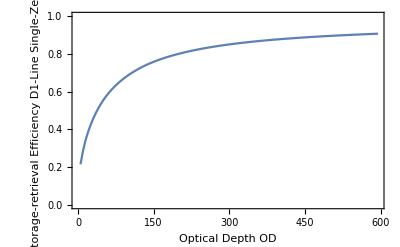

```mathematica
ListPlot[Transpose@{Delete[OD,{{1}}],Chop@Table[NIntegrate[Abs[Interpolation[Transpose@{τ,ftd1l[[i]]},InterpolationOrder->3][t]]^2,{t,-4,4}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,Length[ftd1l]}]},Joined->True,PlotRange->{0,1.0},Frame->True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"Optical Depth OD","Storage-retrieval Efficiency D1-Line Single-Zeeman"}]
```